{{Y[X]→3 X^2+C[1]}}

{3 X^2+C[1]}

{{Y[X]→4+3 X^2}}

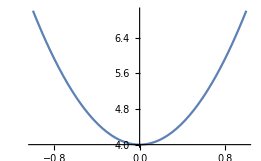

```mathematica
DSolve[{Y'[X]==X*6},Y[X],X]
Y[X]/.DSolve[{Y'[X]==X*6},Y[X],X]
sol=DSolve[{Y'[X]==X*6,Y[0]==4},Y[X],X]
Plot[Y[X]/.sol,{X,-1,1}]
```

{{Y[X]→2-X+Log[Sin[X]]}}

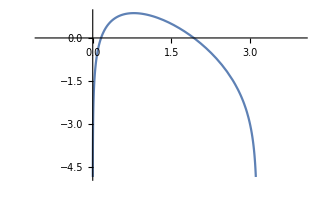

```mathematica
eq:=Y'[X]-Cot[X]+1;
s=DSolve[{eq==0},Y[X],X];
s1=s/.{C[1]-> 2}
Plot[Y[X]/.s1,{X,4,-1}]
```

{{Y[X]→12+6 X+(5 X^10)/2}}

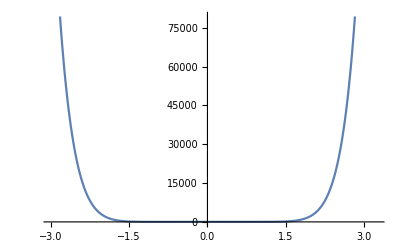

```mathematica
eq=Y'[X]-25X^9;
s=DSolve[{eq==6},Y[X],X];
s1=s/.{C[1]-> 12}
Plot[Y[X]/.s1,{X,-3,3.25}]
```